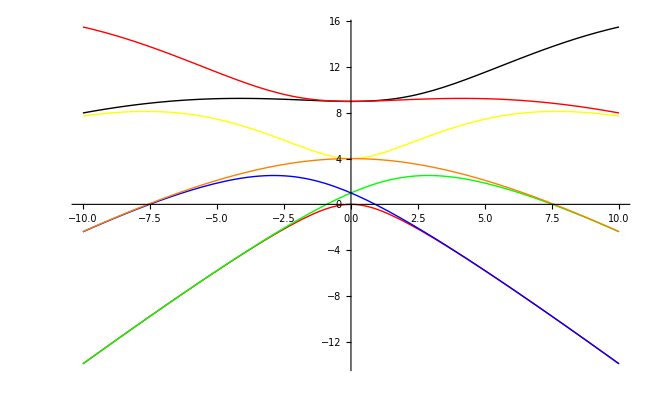

```mathematica
Plot[{MathieuCharacteristicA[0,q],MathieuCharacteristicA[1,q],MathieuCharacteristicB[1,q],MathieuCharacteristicA[2,q],MathieuCharacteristicB[2,q],MathieuCharacteristicA[3,q],MathieuCharacteristicB[3,q]},{q,-10,10},PlotStyle->{Red,Green,Blue,Yellow,Orange,Black}]
```

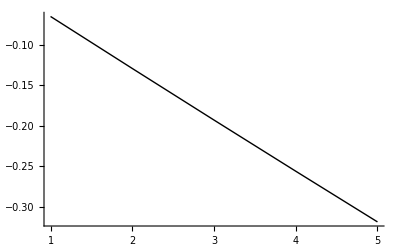

```mathematica
fx[n_,q_]:=(MathieuCharacteristicA[n,q]-MathieuCharacteristicA[0,q])/MathieuCharacteristicA[0,q];
ListPlot[Table[fx[n,1000],{n,1,5}],PlotStyle->{Red,Green,Blue,Yellow,Orange,Black},PlotRange->All,Joined->True]
```

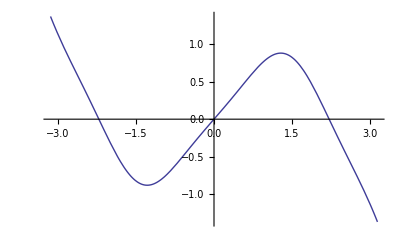

```mathematica
Plot[{Im[MathieuS[1,1,x]]},{x,-π,π}]
```

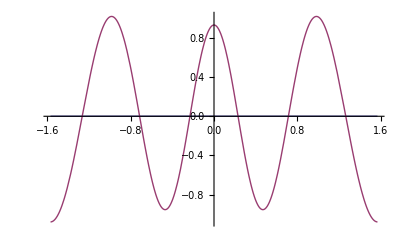

```mathematica
Plot[{0,Re[MathieuC[MathieuCharacteristicA[6,-5],-5,x]]},{x,-π/2,π/2},PlotRange->All]
```

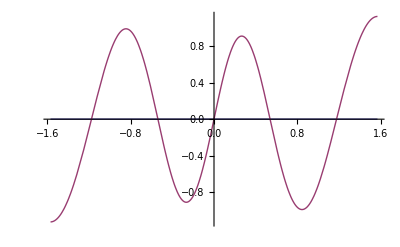

```mathematica
Plot[{0,MathieuS[MathieuCharacteristicB[5,-5],-5,x]},{x,-π/2,π/2},PlotRange->All]
```

```mathematica
N[MathieuS[MathieuCharacteristicB[2,-5],-5,π]]
```

-5.10118×10^-16+6.61744×10^-24 ⅈ

```mathematica
(* Analyzing the coupled oscillator *)
Clear[data,len];
data=Import["POLLT40.dat"];
len=Length[data]
```

10000

```mathematica
Table[data[[n,2]],{n,1,500,10}]
```

{0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806,0.058806}

```mathematica
Clear[av11,av12,av13,av21,av22,av23,av31,av32,av33];
Clear[er11,er12,er13,er21,er22,er23,er31,er32,er33];
Clear[eval,eval1,eval2];
TMAX=10;
For[t=1,t≤TMAX,t++,
Clear[corr11,corr12,corr13,corr21,corr22,corr23,corr31,corr32,corr33];
corr11=Table[data[[n,2]],{n,t,500,10}];
corr12=Table[data[[n,3]],{n,t,500,10}];
corr13=Table[data[[n,4]],{n,t,500,10}];
corr21=Table[data[[n,5]],{n,t,500,10}];
corr22=Table[data[[n,6]],{n,t,500,10}];
corr23=Table[data[[n,7]],{n,t,500,10}];
corr31=Table[data[[n,8]],{n,t,500,10}];
corr32=Table[data[[n,9]],{n,t,500,10}];
corr33=Table[data[[n,10]],{n,t,500,10}];
avg11[t]=Mean[corr11];
err11[t]=Sqrt[StandardDeviation[corr11]/len];
avg12[t]=Mean[corr12];
err12[t]=Sqrt[StandardDeviation[corr12]/len];
avg13[t]=Mean[corr13];
err13[t]=Sqrt[StandardDeviation[corr13]/len];
avg21[t]=Mean[corr21];
err21[t]=Sqrt[StandardDeviation[corr21]/len];
avg22[t]=Mean[corr22];
err22[t]=Sqrt[StandardDeviation[corr22]/len];
avg23[t]=Mean[corr23];
err23[t]=Sqrt[StandardDeviation[corr23]/len];
avg31[t]=Mean[corr31];
err31[t]=Sqrt[StandardDeviation[corr31]/len];
avg32[t]=Mean[corr32];
err32[t]=Sqrt[StandardDeviation[corr32]/len];
avg33[t]=Mean[corr33];
err33[t]=Sqrt[StandardDeviation[corr33]/len];
]
(* Print the correlation matrix *)
For[t=1,t≤TMAX,t++,
Print[t," ",avg11[t]," ",err11[t]];
Print[t," ",avg12[t]," ",err12[t]];
Print[t," ",avg33[t]," ",err33[t]];
Clear[mat];
mat={{avg11[t],avg12[t],avg13[t]},{avg21[t],avg22[t],avg23[t]},{avg31[t],avg32[t],avg33[t]}};
(*Print[MatrixForm[mat]];*)
eval=Eigenvalues[mat];
eval1[t]=eval[[1]];
eval2[t]=eval[[2]];
eval3[t]=eval[[3]];
]
```

1 0.058806 0.

1 0.0029366 0.

1 6.1862×10^-6 2.92512×10^-13

2 0.0034582 0.

2 0.00017269 0.

2 3.827×10^-11 0.

3 0.00020336 0.

3 0.000010155 4.13674×10^-13

3 2.3674×10^-16 0.

4 0.000011959 0.

4 5.9719×10^-7 0.

4 1.4646×10^-21 0.

5 7.0325×10^-7 0.

5 3.5119×10^-8 0.

5 9.0601×10^-27 0.

6 4.1355×10^-8 0.

6 2.0652×10^-9 0.

6 5.6048×10^-32 0.

7 2.432×10^-9 0.

7 1.2145×10^-10 0.

7 3.4673×10^-37 0.

8 1.4301×10^-10 0.

8 7.1417×10^-12 2.85656×10^-16

8 2.1449×10^-42 0.

9 8.4101×10^-12 0.

9 4.1998×10^-13 0.

9 1.3269×10^-47 0.

10 4.9456×10^-13 0.

10 2.4697×10^-14 0.

10 8.2086×10^-53 9.67841×10^-37

{-0.000753815,7.79785×10^-6,5.05429×10^-7,2.97654×10^-8,1.75051×10^-9,1.02941×10^-10,6.05373×10^-12,3.55982×10^-13,2.09338×10^-14,1.23101×10^-15}

{-3.82105×10^-6,1.42486×10^-9,1.36295×10^-12,1.22758×10^-15,1.1049×10^-18,9.94493×10^-22,8.94842×10^-25,8.06647×10^-28,1.00785×10^-30,3.84153×10^-29}

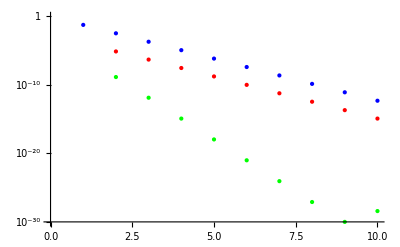

```mathematica
Clear[e1,e2,e3];
e1=Table[eval1[t],{t,1,10}];
e2=Table[-eval2[t],{t,1,10}]
e3=Table[-eval3[t],{t,1,10}]
ListLogPlot[{e1,e2,e3},PlotStyle->{{PointSize[Large],Blue},{PointSize[Large],Red},{PointSize[Large],Green}}]
```

```mathematica
For[i=1,i<TMAX,i++,
Print[i," ",Log[eval1[i]/eval1[i+1]]," ",Log[eval2[i]/eval2[i+1]]];
]
```

1 2.83353 4.5713+3.14159 ⅈ

2 2.83353 2.7362

3 2.83349 2.83206

4 2.83353 2.83344

5 2.83352 2.83351

6 2.83348 2.83348

7 2.83355 2.83355

8 2.83348 2.83352

9 2.83352 2.83353

```mathematica
(BesselI[1,0.01]/BesselI[0,0.01])*(BesselI[-1,0.01]/BesselI[0,0.01])*(BesselI[1,0.02]/BesselI[0,0.02])
```

2.49981×10^-7

```mathematica
(* For the free case, when the oscillators are not coupled *)
Clear[data,c1,c2,c3,m1,m2,m3];
data=Import["POLLT40.dat"];
Length[data]
```

10000

```mathematica
For[t=1,t≤10,t++,
Clear[c];
c=Table[data[[n,2]],{n,t,10000,10}];
c1[t]=Mean[c];
Clear[c];
c=Table[data[[n,6]],{n,t,10000,10}];
c2[t]=Mean[c];
Clear[c];
c=Table[data[[n,10]],{n,t,10000,10}];
c3[t]=Mean[c];
]
```

```mathematica
c1[1]
c2[3]
```

0.98

0.78473

```mathematica
For[i=1,i<10,i++,
m1[i]=Log[c1[i]/c1[i+1]];
m2[i]=Log[c2[i]/c2[i+1]];
m3[i]=Log[c3[i]/c3[i+1]];
(*Print[i," ",Log[c1[[i]]/c1[[i+1]]]," ",Log[c2[[i]]/c2[[i+1]]]," ",Log[c3[[i]]/c3[[i+1]]]];*)
Print[i," ",m2[i]/m1[i]," ",m3[i]/m1[i]];
]
```

1 3.99969 8.99802

2 3.99915 8.99676

3 3.99867 8.99532

4 4.00153 9.00133

5 3.99895 8.99728

6 3.99965 8.99528

7 4.00017 9.00043

8 3.99873 8.9945

9 3.99829 8.99484

```mathematica
b=50.0;
(Log[BesselI[2,b]/BesselI[0,b]]/Log[BesselI[1,b]/BesselI[0,b]])
(Log[BesselI[3,b]/BesselI[0,b]]/Log[BesselI[1,b]/BesselI[0,b]])
```

3.99958

8.99748

```mathematica
Series[BesselI[k,β]/BesselI[0,β],{β,∞,4}]
```

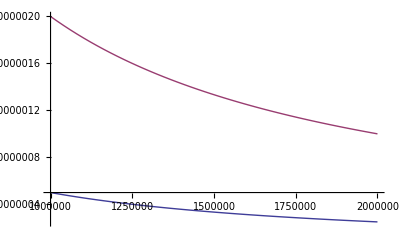

```mathematica
Plot[{-Log[BesselI[1,β]/BesselI[0,β]],-Log[BesselI[2,β]/BesselI[0,β]]},{β,1000000,2000000}]
```

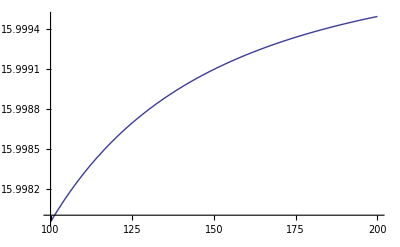

```mathematica
Plot[{Log[BesselI[4,β]/BesselI[0,β]]/Log[BesselI[1,β]/BesselI[0,β]]},{β,100,200}]
```

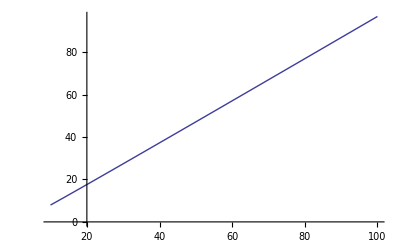

```mathematica
Plot[Log[BesselI[0,β]],{β,10,100}]
```